## Reaction Wheel Inverse Pendulum

```mathematica
(*CreateWindow@PaletteNotebook[{Button["Refresh",vars=Framed[Grid[Select[With[{expr=ToExpression@#},{#,Head[expr],Which[ListQ[expr],Dimensions[expr],NumericQ[expr],expr,StringQ[expr],StringLength[expr],True,"-"]}]&/@Names["Global`*"],(#[[2]]=!=Symbol)&],Alignment->Left],FrameStyle->None,FrameMargins->5]],Dynamic[vars]},WindowElements->{"VerticalScrollBar"},WindowTitle->"Global`*"]*)
```

Required Functions

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
fx=f[t]/2  Cos[α[t]];
fy=f[t]  Cos[α[t]];
bumper[t_] := -0.02 UnitBox[10(t+-31/2)]+0.05 UnitBox[10(t+-21.3)]-0.02 UnitBox[10(t+-26)]
bump[t_] := -0.5Exp[-5(t-4)^(2`20)]+0.5Exp[-5(t-11)^(2`20)]
```

System Variables

```mathematica
displacement = 0.20840734641020697;
ruhelage = π;
verifiedp = {mb->0.0983,mw->0.177,l->0.079886(*0.0921723573499604*),k->0.09,rw->0.00001752037064832828,jw -> 0.00013612480196014234,τ->0.0335,g->9.81,rb->0.00002124166626660119,jb -> 0.000034897779450290215,μ -> 0.00044851844721174985,ι -> 0.1,Θ->0.0025925866007803513 (*0.002303437234648686*)};
```

```mathematica
0.0023487413309206708-mw 0.09^2 - mb l^2 - jw /. verifiedp
```

0.000151588

Make the system equations

```mathematica
r = {l Sin[α[t]], -l Cos[α[t]]};
s = {k Sin[α[t]], -k Cos[α[t]]};
t1 = 1/2 mb D[r,t].D[r,t] + 1/2 mw D[s,t].D[s,t] + 1/2 jb α'[t]^2+ 1/2 jw (α'[t]+ϕ'[t])^2;
(*t1 = 1/2 mb D[r,t].D[r,t] + 1/2 mw D[s,t].D[s,t] + 1/2 jb α'[t]^2+ 1/2 jw (α'[t]+ϕ'[t])^2;*)
v = mb g r[[2]] + mw g s[[2]];
l1 = t1 - v;
```

```mathematica
eqns=EulerEquations[l1, {α[t],ϕ[t]},t] //FullSimplify;
MatrixForm[eqns]
```

(g (l mb+k mw) Sin[α[t]]+(jb+jw+l^2 mb+k^2 mw) α''[t]+jw ϕ''[t]==0
jw (α''[t]+ϕ''[t])==0)

```mathematica
(*deqns={Θ α''[t]+g (l mb+k mw) Sin[α[t]]+jw ϕ''[t]==-rb α'[t]-μ Tanh[α'[t]/ι]+fx+fy,jw (α''[t]+ϕ''[t])==τ u[t]-rw ϕ'[t]};*)
deqns={Θ α''[t]+g (l mb+k mw) Sin[α[t]]+jw ϕ''[t]==-rb α'[t]-μ Tanh[α'[t]/ι]+fx+fy,jw (α''[t]+ϕ''[t])==τ u[t]-rw ϕ'[t]};
```

## State Space Model

Create Linear State Space Model

```mathematica
symmodel=StateSpaceModel[deqns /. {fx -> 0, fy -> 0},{{α[t],π},{α'[t],0},{ϕ'[t],0}},{u[t]},{α[t],α'[t],ϕ'[t]},t] //FullSimplify
```

0100(g (l mb+k mw))/(-jw+Θ)(rb ι+μ)/(jw ι-Θ ι)rw/(-jw+Θ)τ/(jw-Θ)(g (l mb+k mw))/(jw-Θ)(rb+μ/ι)/(-jw+Θ)(rw Θ)/(jw^2-jw Θ)(Θ τ)/(jw (-jw+Θ))100001000010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1331FalseFalseFalseAutomaticNone,{{α[t],0},x_1,{ϕ'[t],0}},{{u[t],0}},Automatic,t

```mathematica
model =StateSpaceModel[deqns,{{α[t],ruhelage},{α'[t],0},{ϕ'[t],0}},{u[t],f[t]},{α[t],α'[t],ϕ'[t]},t,SystemsModelLabels->{{"u","f"},{"α","α'","φ"},{"α","α'","φ"}}] /.verifiedp
```

0100094.9777-1.834520.00713236-13.6375-610.634-94.97771.83452-0.135841259.735610.634100000100000100ufαα'φαα'φStateSpaceModelTrueTrueTrueFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3ufαα'φαα'φIdentityAutomatic23311112212223313233TrueTrueFalseAutomaticufαα'φαα'φ,{{α[t],0},x_1,{ϕ'[t],0}},{{u[t],0},{f[t],0}},Automatic,t

State Space Model Analysis

```mathematica
{matA,matB,matC,matD} = Normal[symmodel] ;
{numA,numB,numC,numD} = Normal[symmodel /. verifiedp];
matK = {{k1, k2, k3}};
matP = {{0},{0},{0}};
GridBox[{{MatrixForm[matA] ,MatrixForm[matB]," "},{MatrixForm[matC],MatrixForm[matD],MatrixForm[matK]}},GridBoxDividers->{"Rows"->{{True}},"Columns"->{{True}}}] //DisplayForm
```

(0 | 1 | 0
(g (l mb+k mw))/(-jw+Θ) | (rb ι+μ)/(jw ι-Θ ι) | rw/(-jw+Θ)
(g (l mb+k mw))/(jw-Θ) | (rb+μ/ι)/(-jw+Θ) | (rw Θ)/(jw^2-jw Θ)) | (0
τ/(jw-Θ)
(Θ τ)/(jw (-jw+Θ))) |  
(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (0
0
0) | (k1 | k2 | k3)

```mathematica
matB//MatrixForm
```

(0
τ/(jw-Θ)
(Θ τ)/(jw (-jw+Θ)))

```mathematica
poles=Eigenvalues[matA] /. verifiedp
ControllableModelQ[model,Method->"Matrix"]
ObservableModelQ[model, Method->"Matrix"]
```

{8.86828,-0.128707,-10.7099}

True

True

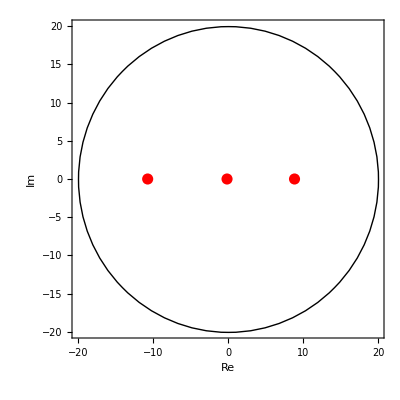

```mathematica
complexplot=ListPlot[{Re[#],Im[#]}&/@poles,AxesOrigin->{0,0},PlotRange->{{-20,20},{-20,20}},AspectRatio->1,Frame->True,RotateLabel->False,FrameLabel->{{Im,None},{Re,"Complex Plane"}},LabelStyle->( FontSize->14),PlotStyle->Directive[Red,PointSize[.02]]];
Show[complexplot,Graphics@Circle[{0,0},20]]
```

LQR Controller design Set Cost and Input Matrices, Create Gains

```mathematica
(*Inverse[r].(numBᵀ.RiccatiSolve[{numA,numB},{q,r,matP}]+matPᵀ) /.verifiedp *)
```

```mathematica
q = DiagonalMatrix[{50,1,0.001}];
(*q = DiagonalMatrix[{0,0,1 10^-2}];*)
r =2{{1}};
lineargains =Join[Last@CoefficientArrays[LQRegulatorGains[{model,1},{q,r}]]//Normal,{ConstantArray[0,3]}];
controlmodel =SystemsModelStateFeedbackConnect[model,lineargains];
{theta,thetadot,phidot} =StateResponse[{controlmodel,{displacement,0,0}},{0,bumper[t]},{t,60}];
output = OutputResponse[{controlmodel,{displacement,0,0}},{0},{t,60}];
controlforce = -lineargains[[1]].{α[t]-π,α'[t],ϕ'[t]};
ssm=NonlinearStateSpaceModel[{{},{controlforce}},{},{{α[t],N@π},α'[t],ϕ'[t]}]
lqresponse = OutputResponse[{ssm},{theta+π,thetadot,phidot},{t,60}];
```

23.8867 (-π+α[t])+2.31488 α'[t]+0.0228898 ϕ'[t]0311NoneNoneFalseFalseFalse{{α[t],3.14159},α'[t],ϕ'[t]}Automatic

Plot OutputResponse and StateResponse

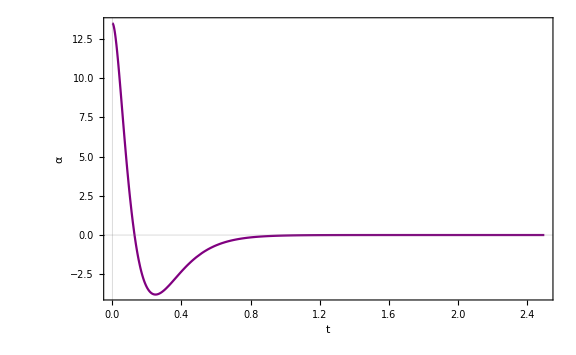

```mathematica
Plot[output[[1]] 180/π ,{t,0,2.5},Evaluated->True,PlotRange->All,PlotTheme->"Scientific",PlotPoints->20,FrameLabel->{t,α,"Output Response"},RotateLabel->False,LabelStyle->FontSize->14, ImageSize->Large, PlotStyle->Purple]
```

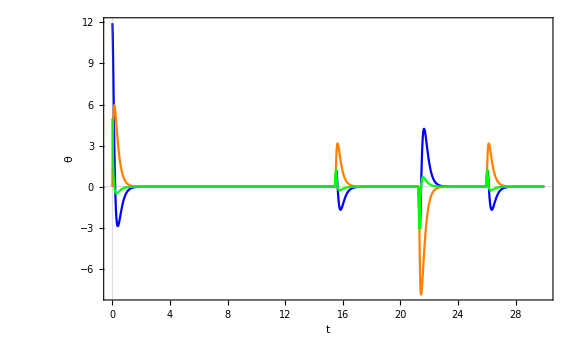
xkcdConvert[-Graphics-]

```mathematica
xkcdConvert@Plot[Evaluate[{theta 180/π,phidot/10,lqresponse}],{t,0,30
},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{t,"θ","State Response"},RotateLabel->False,LabelStyle->FontSize->14,ImageSize->Large, PlotStyle->{{Blue(*,Dashed*)},{Orange(*,DotDashed*)},Green}]
```

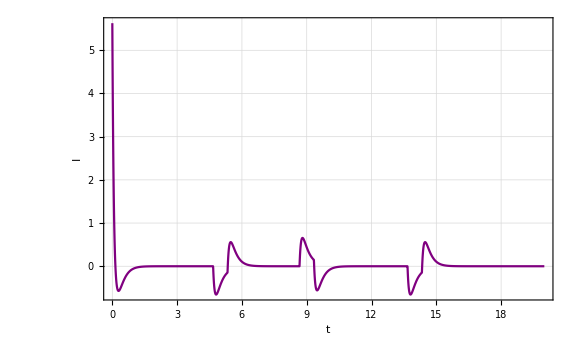
xkcdConvert[-Graphics-]

```mathematica
xkcdConvert@Plot[lqresponse,{t,0,20},PlotRange->All,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{t,"I","LQR Response"},RotateLabel->False,LabelStyle->FontSize->14, ImageSize->Large, PlotStyle->Purple]
```

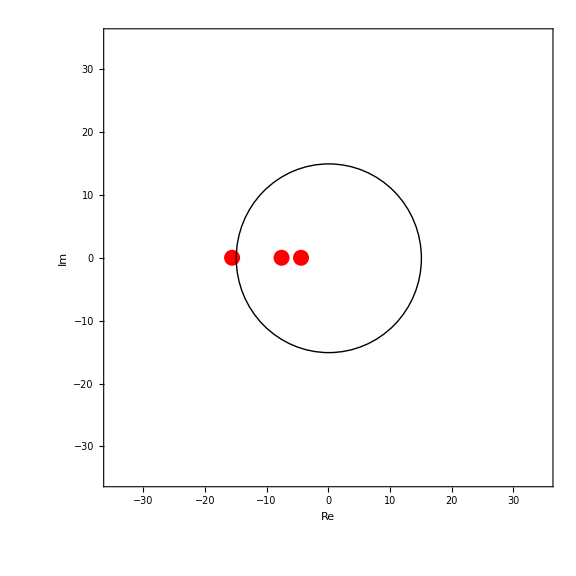
converter[-Graphics-]

```mathematica
complexplotcontrol=ListPlot[{Re[#],Im[#]}&/@Eigenvalues[Normal[controlmodel][[1]]],AxesOrigin->{0,0},PlotRange->{{-35,35},{-35,35}},AspectRatio->1,Frame->True,RotateLabel->False,FrameLabel->{{Im,None},{Re,"Complex Plane"}},LabelStyle->( FontSize->14),PlotStyle->Directive[Red,PointSize[.02]], ImageSize->Large];
converter@Show[complexplotcontrol,Graphics@Circle[{0,0},15]]
```

## Generate Code

```mathematica
Needs["MicrocontrollerKit`"]
```

Create Discrete Models

```mathematica
𝒟 = 10 10^-3;
ssmd = ToDiscreteTimeModel[ssm, 𝒟]
```

23.8867 (-π+α[t])+2.31488 α'[t]+0.0228898 ϕ'[t]1/1000311NoneNoneFalseFalseFalse{{α[t],3.14159},α'[t],ϕ'[t]}Automatic

Generate Code

```mathematica
ℳ=MicrocontrollerEmbedCode[ssmd,<|"Target"->"ArduinoUno","Inputs"->{"A0"->"Analog","A1"->"Analog","A2"->"Analog"},"Outputs"->{"Serial"}|>,<|"ConnectionPort"->None|>,<|"Language"->"Wiring"|>]
Framed[StringTrim[ℳ["SourceCode"]],]
```

MicrocontrollerCodeData[…]

Framed[//========================================
/*  
Generated by: Wolfram Language 12.0.0
Date        : Sun 30 Aug 2020 23:51:37
File        : m000005234591.cpp
  */
//========================================
#include <stdint.h>
#include <avr/interrupt.h>
#include <math.h>
#include <Arduino.h>
double read_adc(uint8_t channel)
{
double adcValue;
switch ( channel)
{
case 0:
adcValue = (5. * analogRead(A0)) / 1023;
break;

case 1:
adcValue = (5. * analogRead(A1)) / 1023;
break;

case 2:
adcValue = (5. * analogRead(A2)) / 1023;
break;
}
return adcValue;
}
double u[3] = {3.141592653589793, 0, 0};
double y[1] = {0.};
void update_nssm(double *u, double *y)
{
y[0] = 23.886653196329103*(-M_PI + u[0]) + 2.314882341444953*u[1] + 0.022889791281586705*u[2];
}
void setup()
{
analogReference(DEFAULT);
Serial.begin(9600);
}
void loop()
{
double uu0 = read_adc(0);
double uu1 = read_adc(1);
double uu2 = read_adc(2);
u[0] = uu0;
u[1] = uu1;
u[2] = uu2;
update_nssm(u, y);
Serial.write(19);
Serial.print(y[0], 2);
Serial.write(17);
delay(10);
},Null]

Steady State Error

```mathematica
matFVT =FullSimplify[Inverse[((z IdentityMatrix[3]) - (matA-matB.matK))].matB];
```

```mathematica
MatrixForm[matFVT]
```

((jw z ι τ)/(g (l mb+k mw) ι (rw+jw z+k3 τ)+z (jw^2 z^2 ι-jw z (z Θ ι+μ)+jw (k1+k2 z) ι τ-(z Θ ι+μ) (rw+k3 τ)-rb ι (rw+jw z+k3 τ)))
(jw z^2 ι τ)/(g (l mb+k mw) ι (rw+jw z+k3 τ)+z (jw^2 z^2 ι-jw z (z Θ ι+μ)+jw (k1+k2 z) ι τ-(z Θ ι+μ) (rw+k3 τ)-rb ι (rw+jw z+k3 τ)))
((g (l mb+k mw) ι-z (rb ι+z Θ ι+μ)) τ)/(g (l mb+k mw) ι (rw+jw z+k3 τ)+z (jw^2 z^2 ι-jw z (z Θ ι+μ)+jw (k1+k2 z) ι τ-(z Θ ι+μ) (rw+k3 τ)-rb ι (rw+jw z+k3 τ))))

```mathematica
Limit[matFVT, z -> 0] // MatrixForm
```

(0
0
τ/(rw+k3 τ))

```mathematica
lineargains
```

{{-23.8867,-2.31488,-0.0228898},{0,0,0}}

```mathematica
τ/(rw+k3 τ) /. verifiedp /. k3 -> -lineargains[[1,3]]
```

42.7117

Adaptive filter

```mathematica
alpha=SystemsModelExtract[controlmodel,{1},{3}]
```

0.1.0.0-230.777-33.4037-0.305027-13.63756109.23603.0915.80944259.7350.0.1.0uφStateSpaceModelTrueTrueFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3uφControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic11311121TrueTrueFalseAutomaticuφ,{{α[t],0},x_1,{ϕ'[t],0}},{Automatic},Automatic,t

```mathematica
pid=TransferFunctionModel[kp+ki/z+kd z,z];
adaptivefilter = SystemsModelFeedbackConnect[alpha,pid]
```

1000000.1.0.0.0.0.0.010000-230.777-33.4037-0.3050270.+13.6375 ki0.-13.6375 kd0.-13.6375 kp-13.63750010006109.23603.0915.809440.-259.735 ki0.+259.735 kd0.+259.735 kp259.7350001000.0.1.0.0.0.0.0000010.0.0.0.1.0.0.0000000.0.1.0.0.1.0.0.0.1.0.0.0.0.uφStateSpaceModelTrueTrueFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5$CellContext`stname6uφControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic11611121TrueTrueTrueAutomaticuφ,{{α[t],0},x_1,{ϕ'[t],0},x_2,x_3,x_4},{Automatic},Automatic,t

```mathematica
Manipulate[Plot[{Evaluate[OutputResponse[adaptivefilter /. {kp -> p, ki -> i,kd -> d},0.1UnitStep[t-0.5],{t,0,2}]],0.1UnitStep[t-0.5]},{t,0,2}],{i,0,10},{p,0,100},{d,0,1}]
```

```mathematica
(*Export["wiring_code.txt",Framed[StringTrim[ℳ2["SourceCode"]],Background->Lighter[LightCyan,0.4]]]*)
```

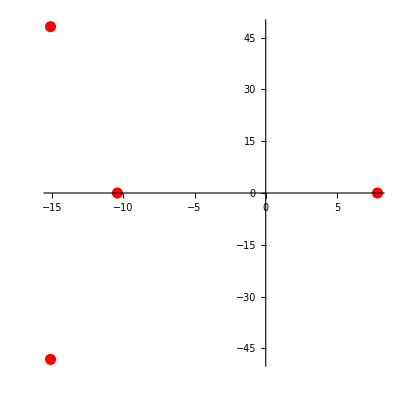

```mathematica
ComplexListPlot[First@TransferFunctionPoles[adaptivefilter/.{kp->0.02,ki->8.92,kd->0}], AspectRatio->1,PlotStyle->Directive[Red,PointSize[.02]]]
```

```mathematica
adaptivefilter
```

1000000.1.0.0.0.0.0.010000-230.777-33.4037-0.3050270.+13.6375 ki0.-13.6375 kd0.-13.6375 kp-13.63750010006109.23603.0915.809440.-259.735 ki0.+259.735 kd0.+259.735 kp259.7350001000.0.1.0.0.0.0.0000010.0.0.0.1.0.0.0000000.0.1.0.0.1.0.0.0.1.0.0.0.0.uφStateSpaceModelTrueTrueFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5$CellContext`stname6uφControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic11611121TrueTrueTrueAutomaticuφ,{{α[t],0},x_1,{ϕ'[t],0},x_2,x_3,x_4},{Automatic},Automatic,t

```mathematica
afilter = pid /. {kd -> 0,ki -> 8.92, kp -> 0.01} //StateSpaceModel
```

0.1.8.920.01StateSpaceModelFalseFalseFalseFalse$CellContext`stname1Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1111FalseFalseFalseAutomaticNoneAutomatic

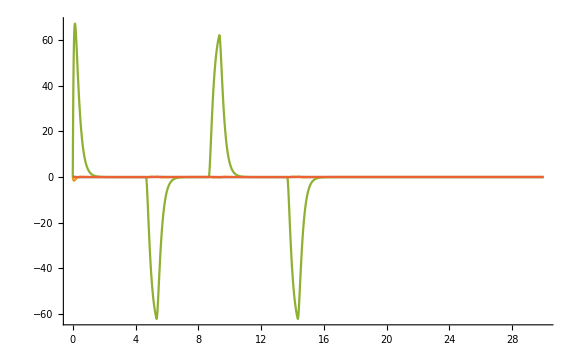

```mathematica
amodel = SystemsModelMerge[SystemsConnectionsModel[{controlmodel,afilter},{{1,1} -> {2,1}},{{1,1},{1,2}},{{2,1},{1,2},{1,3}}]];
{r1,r2,r3,r4}=StateResponse[{amodel,{displacement,0,0,0}},{0,bumper[t]},{t,60}];
Plot[Evaluate[{r1,r2,r3,r4}],{t,0,30},PlotRange->All,ImageSize->Large]
```

```mathematica
adfilter = ToDiscreteTimeModel[afilter,𝒟]
```

1.1.0.08920.05461/100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1111FalseFalseFalseAutomaticNoneAutomatic

```mathematica
ssm
ssmf=NonlinearStateSpaceModel[{{},{controlforce}},{},{xf[t],{α[t],N@π},α'[t],ϕ'[t]}, SamplingPeriod->𝒟]
```

23.8867 (-π+α[t])+2.31488 α'[t]+0.0228898 ϕ'[t]0311NoneNoneFalseFalseFalse{{α[t],3.14159},α'[t],ϕ'[t]}Automatic

23.8867 (-π+α[t])+2.31488 α'[t]+0.0228898 ϕ'[t]1/1000411NoneNoneFalseFalseFalse{xf[t],{α[t],3.14159},α'[t],ϕ'[t]}Automatic

```mathematica
assm=SystemsConnectionsModel[{adfilter,ssmd},{{1,1} -> {2,1}},{{1,1},{2,2},{2,3}(*,{2,4}*)},{{2,1}}]
```

SystemsConnectionsModel[…]

Generate Code

```mathematica
ℳ=MicrocontrollerEmbedCode[assm,<|"Target"->"ArduinoUno","Inputs"->{"A0"->"Analog","A0"->"Analog","A1"->"Analog","A2"->"Analog"},"Outputs"->{"Serial"}|>,<|"ConnectionPort"->None|>,<|"Language"->"Wiring"|>]
Framed[StringTrim[ℳ["SourceCode"]],Background->Darker[Black,0.4]]
```

MicrocontrollerCodeData[…]

//========================================
/*  
Generated by: Wolfram Language 12.0.0
Date        : Sun 30 Aug 2020 23:51:42
File        : m000006234591.cpp
  */
//========================================
#include <stdint.h>
#include <avr/interrupt.h>
#include <math.h>
#include <Arduino.h>
double read_adc(uint8_t channel)
{
double adcValue;
switch ( channel)
{
case 0:
adcValue = (5. * analogRead(A0)) / 1023;
break;

case 1:
adcValue = (5. * analogRead(A0)) / 1023;
break;

case 2:
adcValue = (5. * analogRead(A1)) / 1023;
break;

case 3:
adcValue = (5. * analogRead(A2)) / 1023;
break;
}
return adcValue;
}
double u_0[1] = {0};
double y_0[1] = {0.};
void update_ssm_0(double *u, double *y)
{
static double x[1] = {0};
double x1[1];
y[0] = 0.0892*x[0] + 0.0546*u[0];
x1[0] = 1.*x[0] + 1.*u[0];
x[0] = x1[0];
}
double u_1[3] = {3.141592653589793, 0, 0};
double y_1[1] = {0.};
void update_nssm_1(double *u, double *y)
{
y[0] = 23.886653196329103*(-M_PI + u[0]) + 2.314882341444953*u[1] + 0.022889791281586705*u[2];
}
double u[3] = {0, 0, 0};
double y[1] = {0.};
void update_scm(double *u, double *y)
{
u_0[0] = u[0];
update_ssm_0(u_0, y_0);
u_1[1] = u[1];
u_1[2] = u[2];
u_1[0] = y_0[0];
update_nssm_1(u_1, y_1);
y[0] = y_1[0];
}
void setup()
{
analogReference(DEFAULT);
Serial.begin(9600);
}
void loop()
{
double uu0 = read_adc(0);
double uu1 = read_adc(1);
double uu2 = read_adc(2);
double uu3 = read_adc(3);
u[0] = uu0;
u[1] = uu1;
u[2] = uu2;
u[3] = uu3;
update_scm(u, y);
Serial.write(19);
Serial.print(y[0], 2);
Serial.write(17);
delay(10);
}